```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 250 Kb

{Utilities`CleanSlate`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,System`,Global`}

```mathematica
Clear[ℒ]
ℒ = 1/2 m1 x1'[t]^2+ 1/2 m2 x2'[t]^2- 1/2 k ( x2[t] - x1[t] - l )^2
```

-1/2 k (-l-x1[t]+x2[t])^2+1/2 m1 x1'[t]^2+1/2 m2 x2'[t]^2

```mathematica
Clear[q]
q = { x1[t] , x2[t] }
```

{x1[t],x2[t]}

```mathematica
ℒ // pdConv
```

-1/2 k (-l-x1(t)+x2(t))^2+1/2 m1 ((∂x1(t))/(∂t))^2+1/2 m2 ((∂x2(t))/(∂t))^2

```mathematica
D[ D[ ℒ , D[q[[1]], t] ], t ] - D[ ℒ , q[[1]] ] == 0 
D[ D[ ℒ , D[q[[2]], t] ], t ] - D[ ℒ , q[[2]] ] == 0
```

-k (-l-x1[t]+x2[t])+m1 x1''[t]==0

k (-l-x1[t]+x2[t])+m2 x2''[t]==0

```mathematica
Table[
D[ D[ ℒ , D[q[[i]], t] ], t ] - D[ ℒ , q[[i]] ] == 0 ,
{i,1,2} ]  // TableForm
```

-k (-l-x1[t]+x2[t])+m1 x1''[t]==0
k (-l-x1[t]+x2[t])+m2 x2''[t]==0

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ, q, t ]  ;
eqs // TableForm
```

-k (l+x1[t]-x2[t])-m1 x1''[t]==0
k l+k x1[t]-k x2[t]-m2 x2''[t]==0

```mathematica
Clear[parameters]
parameters = { 
k-> 10 ,
m1 -> 20 , 
m2 -> 30 ,
l-> 2 ,
ℐ -> 100 (* Use [esc] scI [esc} as regular I is imaginary number i *) 
} ;
parameters // TableForm
```

k→10
m1→20
m2→30
l→2
ℐ→100

```mathematica
eqs /. parameters // TableForm
```

-10 (2+x1[t]-x2[t])-20 x1''[t]==0
20+10 x1[t]-10 x2[t]-30 x2''[t]==0

```mathematica
Clear[ics]
ics = { 
x1[0] == 0 , 
x1'[0] == ℐ/m1 , (* Impulse divided by m1 *) 
x2[0] == l ,
x2'[0] == 0 
} ;
ics // TableForm
```

x1[0]==0
x1'[0]==ℐ/m1
x2[0]==l
x2'[0]==0

```mathematica
ics /. parameters  // TableForm
```

x1[0]==0
x1'[0]==5
x2[0]==2
x2'[0]==0

```mathematica
Clear[solution]
solution[t_] = 
First[NDSolve[ Union[ eqs /. parameters , ics /. parameters ] , q, { t, 0, 100 } ]]
```

{x1[t]→InterpolatingFunction[…][t],x2[t]→InterpolatingFunction[…][t]}

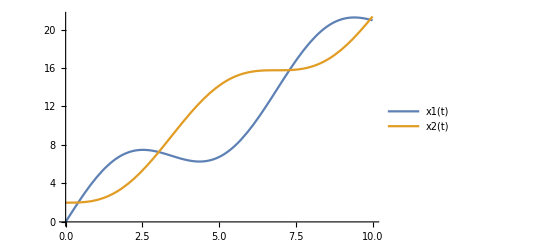

```mathematica
Plot[ Evaluate[ q /. solution[t] ]  , { t, 0, 10 } , PlotLegends->  q ]
```

```mathematica
?PlotLegends
```

```mathematica
solution[t]
solution[t][[1]]
solution[t][[1,2]]
```

{x1[t]→InterpolatingFunction[…][t],x2[t]→InterpolatingFunction[…][t]}

x1[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

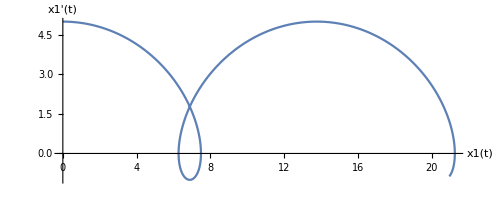

```mathematica
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, 10 } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]
```

```mathematica
solution[t]
solution[t][[2]]
solution[t][[2,2]]
```

{x1[t]→InterpolatingFunction[…][t],x2[t]→InterpolatingFunction[…][t]}

x2[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

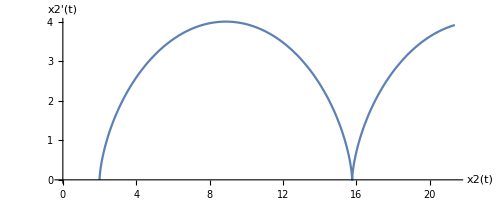

```mathematica
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t , 0, 10 } , AxesLabel-> { q[[2]] , D[q[[2]], t] } ]
```

```mathematica
ParametricPlot3D[ { solution[t][[2,2]] , solution'[t][[2,2]]  , t } , { t , 0, 10 } , AxesLabel-> { q[[2]] , D[q[[2]], t] , t  } ]
```

-Graphics3D-